```mathematica
AppendTo[$Path,"/Users/scott/projects/toolkit/algebra-spiders/src/main/mathematica/"];
```

```mathematica
<<Spiders`
```

Loading Spiders` version 2015-06-18 ...

```mathematica
ImageCrop[ImageCrop[ImageRotate[Import["~/projects/exceptional/notes/bases.pdf"]⟦1⟧],{Full,500}],{Full,275},Top]
```

-Graphics-

```mathematica
S=PlanarGraphs@spider[]
```

«JavaObject[net.tqft.toolkit.algebra.spiders.DiagramSpider$$anon$1]»

```mathematica
DrawPlanarGraph/@(basis0=ReducedDiagrams[BraidedTrivalent⟦1⟧,6,0,0])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis1=Table[S@rotate[S@tensor[PlanarGraphs@crossing[],PlanarGraphs@strand[]],k],{k,0,5}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis2=Table[S@rotate[S@multiply[PlanarGraphs@crossing[],PlanarGraphs@inverseCrossing[],1],k],{k,0,2}])
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis3={PlanarGraphs@Reidemeister3[]@head[]})
```

{-Graphics-}

```mathematica
DrawPlanarGraph/@(basis4=ReducedDiagrams[BraidedTrivalent⟦1⟧,6,0,2])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis5=Table[S@rotate[S@multiply[S@rotate[S@multiply[PlanarGraphs@crossing[],PlanarGraphs@trivalentVertex[],1],2],PlanarGraphs@trivalentVertex[],1],k],{k,0,5}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis6={S@multiply[PlanarGraphs@inverseCrossing[],S@rotate[S@multiply[PlanarGraphs@crossing[],S@rotate[S@tensor[PlanarGraphs@trivalentVertex[],PlanarGraphs@trivalentVertex[]],1],2],3],2]})
```

{-Graphics-}

```mathematica
DrawPlanarGraph/@(basis7=Table[S@rotate[S@multiply[PlanarGraphs@I[],PlanarGraphs@crossing[],1],k],{k,0,5}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis8=Table[S@rotate[S@multiply[PlanarGraphs@H[],PlanarGraphs@crossing[],1],k],{k,0,5}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis9=Table[S@rotate[S@multiply[S@rotate[S@multiply[PlanarGraphs@crossing[],PlanarGraphs@inverseCrossing[],1],2],PlanarGraphs@H[],2],k],{k,0,2}])
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis10=Table[S@rotate[S@multiply[S@rotate[S@multiply[PlanarGraphs@inverseCrossing[],PlanarGraphs@trivalentVertex[],1],3],PlanarGraphs@trivalentVertex[],1],k],{k,0,2}])
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis11=Cases[ReducedDiagrams[BraidedTrivalent⟦1⟧,6,0,4],g_/;!(g@Subgraphs[]@apply[polygon[4]]@excisions[]@hasNext[])])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis12=Table[S@rotate[S@multiply[S@rotate[S@multiply[S@rotate[S@multiply[PlanarGraphs@crossing[],PlanarGraphs@trivalentVertex[],1],2],PlanarGraphs@trivalentVertex[],1],5],PlanarGraphs@I[],2],k],{k,0,5}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis13=Table[S@rotate[S@multiply[PlanarGraphs@fromString["PlanarGraph(14,Vector(List((8,14), (9,15), (7,16), (6,18), (5,19), (10,17)), List((5,17), (11,19), (13,15)), List((6,19), (12,18), (11,15)), List((8,15), (10,14), (13,17)), List((7,18), (9,16), (12,15))),List((1,0), (1,0), (1,0), (1,0)),0)"],PlanarGraphs@crossing[],2],k],{k,0,3}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis14={polygon[6]})
```

{-Graphics-}

```mathematica
basis=basis0~Join~basis1~Join~basis2~Join~basis3~Join~basis4~Join~basis5~Join~basis6~Join~basis7~Join~basis8~Join~basis9~Join~basis10~Join~basis11~Join~basis12~Join~basis13~Join~basis14;
```

```mathematica
Length[basis]
```

80

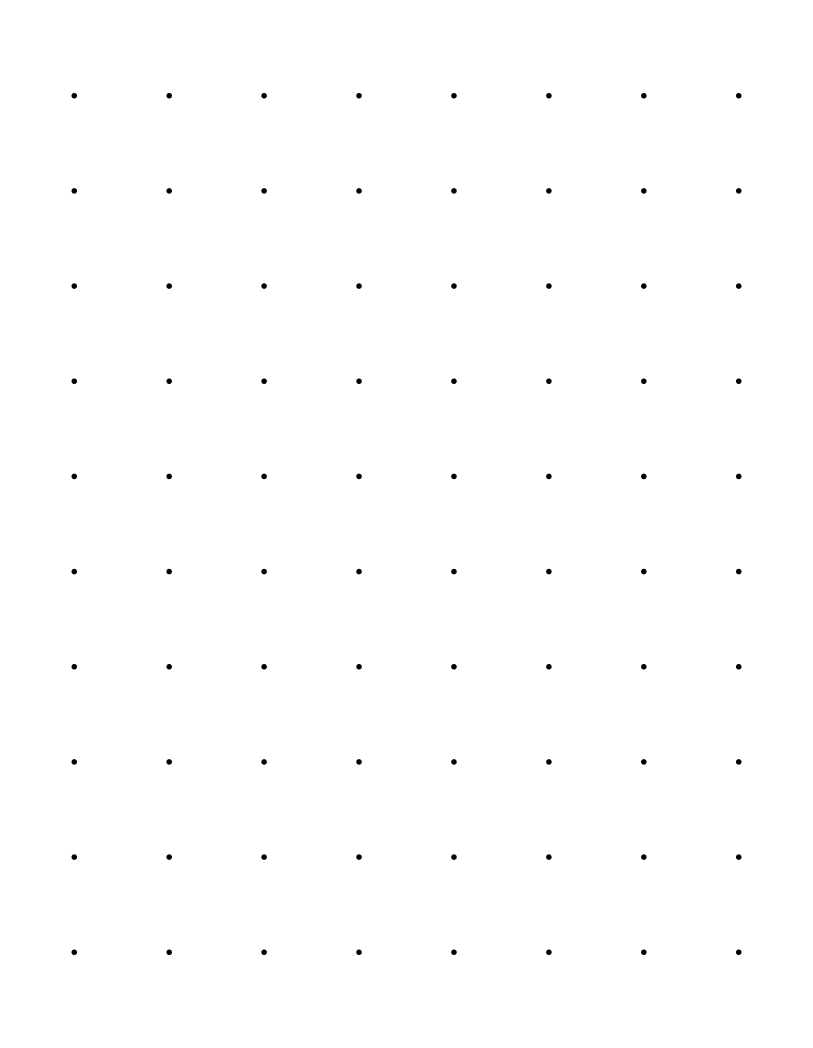

```mathematica
GraphicsGrid[Partition[DrawPlanarGraph/@basis,8]]
```

```mathematica
closed=Union[Flatten[Outer[S@multiply[#1,#2,6]&,basis,basis]]]
```

{«JavaObject[net.tqft.toolkit.algebra.spiders.PlanarGraph]»,«JavaObject[net.tqft.toolkit.algebra.spiders.PlanarGraph]»,«JavaObject[net.tqft.toolkit.algebra.spiders.PlanarGraph]»,«JavaObject[net.tqft.toolkit.algebra.spiders.PlanarGraph]»,«JavaObject[net.tqft.toolkit.algebra.spiders.PlanarGraph]»,6391,«JavaObject[net.tqft.toolkit.algebra.spiders.PlanarGraph]»,«JavaObject[net.tqft.toolkit.algebra.spiders.PlanarGraph]»,«JavaObject[net.tqft.toolkit.algebra.spiders.PlanarGraph]»,«JavaObject[net.tqft.toolkit.algebra.spiders.PlanarGraph]»}
 |  |  |  |

```mathematica
Length/@Table[Symbol["basis"<>ToString[k]],{k,0,14}]
```

{5,6,3,1,15,6,1,6,6,3,3,14,6,4,1}

```mathematica
Total[%]
```

80